```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
dataLin=Table[{n,n/n},{n,1,10}]
dataQuad=Table[{n,n^2/n},{n,1,10}]
dataExp=Table[{n,2^n/n},{n,1,10}]
```

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1}}

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10}}

{{1,2},{2,2},{3,8/3},{4,4},{5,32/5},{6,32/3},{7,128/7},{8,32},{9,512/9},{10,512/5}}

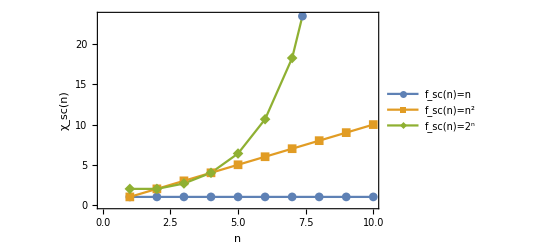

```mathematica
ListLinePlot[{dataLin,dataQuad,dataExp},PlotMarkers->Automatic,Frame->True,FrameLabel->{"n","χ_sc(n)"},BaseStyle->{FontSize->14},PlotLegends->Placed[{"f_sc(n)=n","f_sc(n)=n^2","f_sc(n)=2^n"},{0.25,0.6}]]
```